## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
(*Q10 = 2.5; Average factor for biological systems*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "GAPD_param_inf";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Desktop/MD/kinetics/GAPD/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi
"[nad,g3p,pi,1,3-diphosphoglycerate,nadh]"

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModel["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1}
```

{{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}}

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList,
						 otherMetsReverseZeroSub, otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{g3p^c→0,nad^c→0,pi^c→0}

{(13dpg)^c→0,nadh^c→0}

{g3p^c→∞,nad^c→∞,pi^c→∞}

{(13dpg)^c→∞,nadh^c→∞}

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
haldaneRatiosList
```

{(k_GAPD1^⟶ k_GAPD2^⟶ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶)/(k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD3^⟵ k_GAPD4^⟵ k_GAPD5^⟵ k_GAPD6^⟵)}

## Semi-Automated Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵),1.09*10^-6 ,{6.7*10^-10, 0.0018}}};
customRatiosDataList
```

{{1,(k_GAPD1^⟶ k_GAPD2^⟶ k_GAPD3^⟶ k_GAPD4^⟶)/(k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD3^⟵ k_GAPD4^⟵),1.09×10^-6,{6.7×10^-10,0.0018}}}

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

{0.00156875,0.00156875,0.00156875}

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_inf/input/customRatio_1.txt"	1.09e-6

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter influence

```mathematica
dataFileName = "GAPD_all";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "GAPD_dKd";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp={};
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "GAPD_Keq";
KeqListTemp={};
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "GAPD_Km1";
KeqListTemp=KeqList;
kmListTemp=kmList[[2;;]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];


dataFileName = "GAPD_Km2";
KeqListTemp=KeqList;
kmListTemp={kmList[[1]], kmList[[3]]};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];


dataFileName = "GAPD_Km3";
KeqListTemp=KeqList;
kmListTemp=kmList[[;;2]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];


dataFileName = "GAPD_kcat";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = {};
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "GAPD_Kd";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = {};

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Part::partw: Part 1 of {} does not exist.

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating custom ratios data...

### Parameter scan

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,1.09*10^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«23 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 2.80668765835
best_fit: 1.07230376322
best_fit: 0.998882608959
best_fit: 2.81549125443
best_fit: 0.752890896194

## Pull in Parameters and Check Fit and Enzyme Statistics for param_scan

```mathematica
outputPath
```

/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/output

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,1.09*10^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

nEnsembles=10;

flagFitType = "abs_ssd";
errorList = {};
Do[
Do[

fitDescription = paramScan[[1]] <>"_"<>ToString[paramScan[[2]]]<>"_"<> ToString[N@AccountingForm[paramVal]];
ssdList = 
Table[

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> "_"<>ToString@ensembleI<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "GAPD_"<> fitDescription<>".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription];
Print@{paramVal, filteredDataList[[1,1]]};
ToString[N@AccountingForm[filteredDataList[[1,1]]]],

{ensembleI, Range[nEnsembles]}];

Print[ssdList];
AppendTo[errorList, Flatten@{ToString[N@AccountingForm[paramVal]], ssdList}];,

{paramVal, paramScan[[3]]}];,
{paramScan, paramScanList}];

Export[ FileNameJoin[{outputPath, "treated_data", "param_scan_ssd.csv"}, OperatingSystem->$OperatingSystem],errorList, "TSV"];
```

```mathematica
errorList//TableForm
```

customRatio_1 | 0.000000000001 | 0.00000000102726
customRatio_1 | 0.00000000001 | 0.00000000042135
customRatio_1 | 0.0000000001 | 0.0000000000102364
customRatio_1 | 0.000000001 | 0.0000000000066693
customRatio_1 | 0.00000001 | 0.00000000000145757
customRatio_1 | 0.0000001 | 0.00000000000344528
customRatio_1 | 0.000001 | 0.00000000000166854
customRatio_1 | 0.00000109 | 0.00000000000443924
customRatio_1 | 0.00001 | 0.000000000000105293
customRatio_1 | 0.0001 | 0.0000000000000000000461147
customRatio_1 | 0.001 | 0.0000000000000000162621
customRatio_1 | 0.01 | 0.00000000000000245293
customRatio_1 | 0.1 | 0.0000000000000000243629
customRatio_1 | 1. | 0.00000000000000000325224
customRatio_1 | 10. | 0.00000000000000000593573
customRatio_1 | 100. | 0.000000000000000197496
customRatio_1 | 1000. | 0.311466
customRatio_1 | 10000. | 5.99475
customRatio_1 | 100000. | 493.835
customRatio_1 | 1000000. | 47447.5
customRatio_1 | 10000000. | 657266.
customRatio_1 | 100000000. | 788019.
customRatio_1 | 1000000000. | 790041.
customRatio_1 | 10000000000. | 790071.
customRatio_1 | 100000000000. | 790072.
customRatio_1 | 1000000000000. | 790074.

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | haldaneRatio_1 | 4.55934 | 20.7876 | 0.451988 | 99.9972 | 0.452 | 0.000012468
1 | relRateFor_nad | 1.04138 | 1.08448 | 0.909065 | 999.972 | 0.0909091 | 0.999974
1 | relRateFor_nad | 0.863885 | 0.746297 | 0.863177 | 630.946 | 0.136807 | 0.999984
1 | relRateFor_nad | 0.697318 | 0.486253 | 0.79923 | 398.102 | 0.20076 | 0.99999
1 | relRateFor_nad | 0.545538 | 0.297611 | 0.715246 | 251.186 | 0.284747 | 0.999994
1 | relRateFor_nad | 0.412441 | 0.170107 | 0.613133 | 158.488 | 0.386863 | 0.999996
1 | relRateFor_nad | 0.301029 | 0.0906184 | 0.499997 | 99.9995 | 0.5 | 0.999997
1 | relRateFor_nad | 0.212442 | 0.0451316 | 0.386862 | 63.0955 | 0.613137 | 0.999998
1 | relRateFor_nad | 0.14554 | 0.0211819 | 0.284746 | 39.8106 | 0.715253 | 0.999999
1 | relRateFor_nad | 0.0973225 | 0.00947167 | 0.200759 | 25.1188 | 0.79924 | 0.999999
1 | relRateFor_nad | 0.0638919 | 0.00408217 | 0.136806 | 15.8489 | 0.863193 | 1.
1 | relRateFor_nad | 0.0413926 | 0.00171335 | 0.0909088 | 9.99997 | 0.909091 | 1.
1 | relRateFor_g3p | 0.43838 | 0.192177 | 0.158543 | 174.398 | 0.0909091 | 0.249452
1 | relRateFor_g3p | 0.401732 | 0.161388 | 0.208209 | 152.192 | 0.136807 | 0.345016
1 | relRateFor_g3p | 0.355331 | 0.12626 | 0.254237 | 126.637 | 0.20076 | 0.454997
1 | relRateFor_g3p | 0.301072 | 0.0906446 | 0.284803 | 100.02 | 0.284747 | 0.56955
1 | relRateFor_g3p | 0.243103 | 0.0590992 | 0.290249 | 75.0263 | 0.386863 | 0.677112
1 | relRateFor_g3p | 0.186793 | 0.0348918 | 0.268711 | 53.7423 | 0.5 | 0.768711
1 | relRateFor_g3p | 0.136954 | 0.0187563 | 0.227311 | 37.0735 | 0.613137 | 0.840448
1 | relRateFor_g3p | 0.0964071 | 0.00929432 | 0.177778 | 24.8553 | 0.715253 | 0.893031
1 | relRateFor_g3p | 0.0656812 | 0.00431402 | 0.130493 | 16.3272 | 0.79924 | 0.929733
1 | relRateFor_g3p | 0.0436609 | 0.00190627 | 0.0912914 | 10.576 | 0.863193 | 0.954484
1 | relRateFor_g3p | 0.0285184 | 0.000813301 | 0.0617001 | 6.78701 | 0.909091 | 0.970791
1 | relRateFor_pi | 17.4074 | 303.019 | 0.0909091 | 100. | 0.0909091 | 3.55764×10^-19
1 | relRateFor_pi | 17.3849 | 302.236 | 0.136807 | 100. | 0.136807 | 5.63848×10^-19
1 | relRateFor_pi | 17.3515 | 301.075 | 0.20076 | 100. | 0.20076 | 8.9364×10^-19
1 | relRateFor_pi | 17.3033 | 299.404 | 0.284747 | 100. | 0.284747 | 1.41632×10^-18
1 | relRateFor_pi | 17.2364 | 297.093 | 0.386863 | 100. | 0.386863 | 2.24472×10^-18
1 | relRateFor_pi | 17.1478 | 294.047 | 0.5 | 100. | 0.5 | 3.55764×10^-18
1 | relRateFor_pi | 17.0364 | 290.239 | 0.613137 | 100. | 0.613137 | 5.63848×10^-18
1 | relRateFor_pi | 16.9033 | 285.721 | 0.715253 | 100. | 0.715253 | 8.9364×10^-18
1 | relRateFor_pi | 16.7515 | 280.613 | 0.79924 | 100. | 0.79924 | 1.41632×10^-17
1 | relRateFor_pi | 16.5849 | 275.06 | 0.863193 | 100. | 0.863193 | 2.24472×10^-17
1 | relRateFor_pi | 16.4074 | 269.204 | 0.909091 | 100. | 0.909091 | 3.55764×10^-17
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | absRateFor | 24.6095 | 605.628 | 268. | 100. | 268 | 6.58593×10^-23
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | KdRatio_nad | 0.922313 | 0.850661 | 2.81732×10^-7 | 88.0412 | 3.2×10^-7 | 3.82681×10^-8
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12
1 | customRatio_1 | 0. | 0. | 0.000488281 | 4.88281×10^-14 | 1.×10^12 | 1.×10^12

### Simulated Data and Best Fit Data Plot

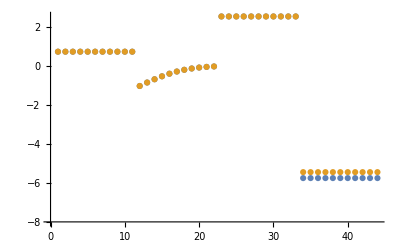

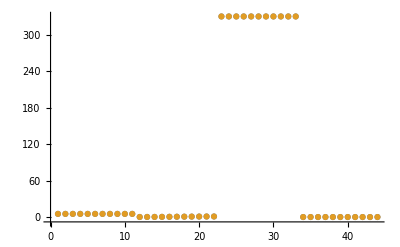

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Pull in Parameters and Check Fit and Enzyme Statistics for param_inf

```mathematica
paramList={"all", "dKd", "kcat", "Keq", "Km1", "Km2", "Km3", "Kd"};
nEnsembles = 99;

flagFitType = "abs_ssd";

Do[
Do[

fitDescription = param <>"_"<>ToString[fitI];

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "GAPD_"<> param<> ".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription];,

{fitI, 0, nEnsembles}],
{param, paramList}];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | relRateFor_2pg | 4.72843×10^-7 | 2.2358×10^-13 | 9.89783×10^-8 | 0.000108876 | 0.0909091 | 0.0909092
1 | relRateFor_2pg | 4.4897×10^-7 | 2.01574×10^-13 | 1.4143×10^-7 | 0.000103379 | 0.136807 | 0.136807
1 | relRateFor_2pg | 4.15706×10^-7 | 1.72812×10^-13 | 1.92167×10^-7 | 0.00009572 | 0.20076 | 0.20076
1 | relRateFor_2pg | 3.72022×10^-7 | 1.38401×10^-13 | 2.43918×10^-7 | 0.0000856614 | 0.284747 | 0.284747
1 | relRateFor_2pg | 3.18909×10^-7 | 1.01703×10^-13 | 2.8408×10^-7 | 0.0000734316 | 0.386863 | 0.386863
1 | relRateFor_2pg | 2.60064×10^-7 | 6.76331×10^-14 | 2.99409×10^-7 | 0.0000598819 | 0.5 | 0.5
1 | relRateFor_2pg | 2.01218×10^-7 | 4.04887×10^-14 | 2.8408×10^-7 | 0.0000463322 | 0.613137 | 0.613137
1 | relRateFor_2pg | 1.48105×10^-7 | 2.1935×10^-14 | 2.43918×10^-7 | 0.0000341024 | 0.715253 | 0.715253
1 | relRateFor_2pg | 1.04421×10^-7 | 1.09037×10^-14 | 1.92167×10^-7 | 0.0000240438 | 0.79924 | 0.79924
1 | relRateFor_2pg | 7.1157×10^-8 | 5.06331×10^-15 | 1.4143×10^-7 | 0.0000163845 | 0.863193 | 0.863193
1 | relRateFor_2pg | 4.72843×10^-8 | 2.2358×10^-15 | 9.89782×10^-8 | 0.0000108876 | 0.909091 | 0.909091
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6

### Simulated Data and Best Fit Data Plot

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

-Graphics-

-Graphics-

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

-Graphics-

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

-Graphics-

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

-Graphics-

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

-Graphics-

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/GAPD.dat⟦2⟧ is longer than depth of object.

Part::partd: Part specification \"\</home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/GAPD.dat\>\"⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | relRateFor_nad | 1.05693×10^-12 | 1.11711×10^-24 | 2.21226×10^-13 | 2.43348×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_nad | 1.0032×10^-12 | 1.00641×10^-24 | 3.16053×10^-13 | 2.31021×10^-10 | 0.136807 | 0.136807
1 | relRateFor_nad | 9.29146×10^-13 | 8.63312×10^-25 | 4.29518×10^-13 | 2.13946×10^-10 | 0.20076 | 0.20076
1 | relRateFor_nad | 8.31446×10^-13 | 6.91302×10^-25 | 5.4512×10^-13 | 1.9144×10^-10 | 0.284747 | 0.284747
1 | relRateFor_nad | 7.12708×10^-13 | 5.07952×10^-25 | 6.34881×10^-13 | 1.6411×10^-10 | 0.386863 | 0.386863
1 | relRateFor_nad | 5.81202×10^-13 | 3.37795×10^-25 | 6.69131×10^-13 | 1.33826×10^-10 | 0.5 | 0.5
1 | relRateFor_nad | 4.49724×10^-13 | 2.02251×10^-25 | 6.34937×10^-13 | 1.03555×10^-10 | 0.613137 | 0.613137
1 | relRateFor_nad | 3.30985×10^-13 | 1.09551×10^-25 | 5.4512×10^-13 | 7.62135×10^-11 | 0.715253 | 0.715253
1 | relRateFor_nad | 2.33411×10^-13 | 5.44805×10^-26 | 4.29545×10^-13 | 5.37442×10^-11 | 0.79924 | 0.79924
1 | relRateFor_nad | 1.59039×10^-13 | 2.52935×10^-26 | 3.1608×10^-13 | 3.66176×10^-11 | 0.863193 | 0.863193
1 | relRateFor_nad | 1.05596×10^-13 | 1.11505×10^-26 | 2.21045×10^-13 | 2.4315×10^-11 | 0.909091 | 0.909091
1 | relRateFor_g3p | 2.17788×10^-11 | 4.74316×10^-22 | 4.55888×10^-12 | 5.01477×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_g3p | 2.06792×10^-11 | 4.27631×10^-22 | 6.51415×10^-12 | 4.76157×10^-9 | 0.136807 | 0.136807
1 | relRateFor_g3p | 1.91472×10^-11 | 3.66617×10^-22 | 8.85111×10^-12 | 4.4088×10^-9 | 0.20076 | 0.20076
1 | relRateFor_g3p | 1.71351×10^-11 | 2.93611×10^-22 | 1.12347×10^-11 | 3.94551×10^-9 | 0.284747 | 0.284747
1 | relRateFor_g3p | 1.46888×10^-11 | 2.15761×10^-22 | 1.30845×10^-11 | 3.38221×10^-9 | 0.386863 | 0.386863
1 | relRateFor_g3p | 1.19784×10^-11 | 1.43483×10^-22 | 1.37906×10^-11 | 2.75813×10^-9 | 0.5 | 0.5
1 | relRateFor_g3p | 9.26789×10^-12 | 8.58938×10^-23 | 1.30844×10^-11 | 2.13401×10^-9 | 0.613137 | 0.613137
1 | relRateFor_g3p | 6.82163×10^-12 | 4.65346×10^-23 | 1.12347×10^-11 | 1.57073×10^-9 | 0.715253 | 0.715253
1 | relRateFor_g3p | 4.80951×10^-12 | 2.31314×10^-23 | 8.85103×10^-12 | 1.10743×10^-9 | 0.79924 | 0.79924
1 | relRateFor_g3p | 3.27746×10^-12 | 1.07418×10^-23 | 6.51423×10^-12 | 7.54667×10^-10 | 0.863193 | 0.863193
1 | relRateFor_g3p | 2.17801×10^-12 | 4.74372×10^-24 | 4.55913×10^-12 | 5.01504×10^-10 | 0.909091 | 0.909091
1 | relRateFor_pi | 1.21145×10^-11 | 1.46762×10^-22 | 2.53586×10^-12 | 2.78945×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_pi | 1.15028×10^-11 | 1.32314×10^-22 | 3.62352×10^-12 | 2.64864×10^-9 | 0.136807 | 0.136807
1 | relRateFor_pi | 1.06508×10^-11 | 1.1344×10^-22 | 4.92351×10^-12 | 2.45243×10^-9 | 0.20076 | 0.20076
1 | relRateFor_pi | 9.53138×10^-12 | 9.08471×10^-23 | 6.24933×10^-12 | 2.1947×10^-9 | 0.284747 | 0.284747
1 | relRateFor_pi | 8.17069×10^-12 | 6.67601×10^-23 | 7.27834×10^-12 | 1.88137×10^-9 | 0.386863 | 0.386863
1 | relRateFor_pi | 6.66311×10^-12 | 4.43971×10^-23 | 7.6712×10^-12 | 1.53424×10^-9 | 0.5 | 0.5
1 | relRateFor_pi | 5.15532×10^-12 | 2.65773×10^-23 | 7.27829×10^-12 | 1.18706×10^-9 | 0.613137 | 0.613137
1 | relRateFor_pi | 3.79452×10^-12 | 1.43984×10^-23 | 6.24933×10^-12 | 8.73724×10^-10 | 0.715253 | 0.715253
1 | relRateFor_pi | 2.67536×10^-12 | 7.15755×10^-24 | 4.92351×10^-12 | 6.16023×10^-10 | 0.79924 | 0.79924
1 | relRateFor_pi | 1.82306×10^-12 | 3.32353×10^-24 | 3.62343×10^-12 | 4.19771×10^-10 | 0.863193 | 0.863193
1 | relRateFor_pi | 1.21139×10^-12 | 1.46747×10^-24 | 2.53575×10^-12 | 2.78932×10^-10 | 0.909091 | 0.909091
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6

### Simulated Data and Best Fit Data Plot

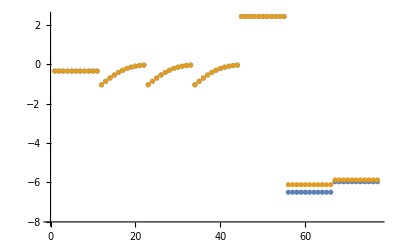

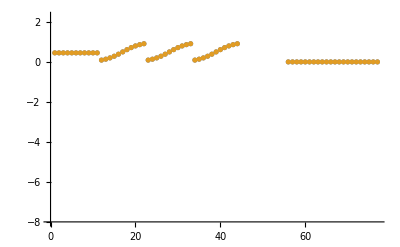

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

-Graphics-

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

-Graphics-

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

-Graphics-

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

-Graphics-

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10